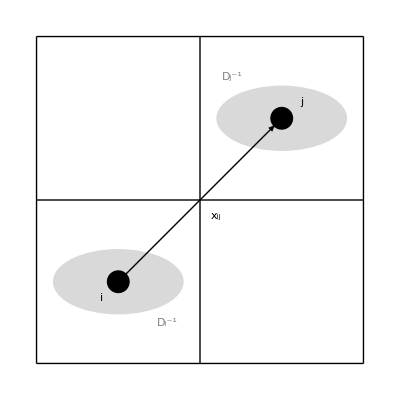

```mathematica
Graphics[{

Black,
Table[Line[{{i,1},{i,3}}],{i,1,3}],
Table[Line[{{1,i},{3,i}}],{i,1,3}],

LightGray,
Disk[{1.5,1.5},{0.4,0.2}],
Disk[{2.5,2.5},{0.4,0.2}],

Thick,Black,

Arrow[{{1.5,1.5},{2.46,2.46}}],

Black,
Disk[{2.5,2.5},{0.07,0.07}],
Disk[{1.5,1.5},{0.07,0.07}],

Inset[Style["x_ij",Large],{2.1,1.9}],
Inset[Style["i",Large],{1.4,1.4}],
Inset[Style["j",Large],{2.62,2.6}],
Inset[Style["D_i^-1",Large,Gray],{1.8,1.25}],
Inset[Style["D_j^-1",Large,Gray],{2.2,2.75}]
}]
```

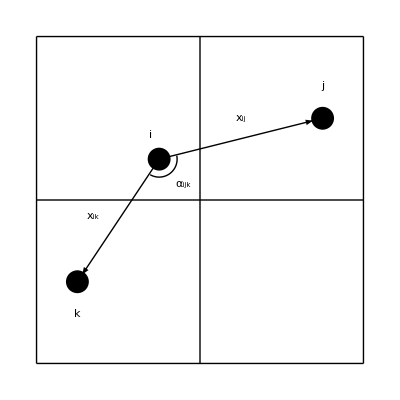

```mathematica
Graphics[{

Black,
Table[Line[{{i,1},{i,3}}],{i,1,3}],
Table[Line[{{1,i},{3,i}}],{i,1,3}],

Thick,Black,

Arrow[{{1.75,2.25},{1.75,2.25} + ({2.75,2.5} -{1.75,2.25})*0.94}],
Arrow[{{1.75,2.25},{1.75,2.25} + ({1.25,1.5} -{1.75,2.25})*0.94}],

Black,
Disk[{2.75,2.5},{0.07,0.07}],
Disk[{1.25,1.5},{0.07,0.07}],
Disk[{1.75,2.25},{0.07,0.07}],

Inset[Style["x_ij",Large],{2.25,2.5}],
Inset[Style["x_ik",Large],{1.35,1.9}],
Inset[Style["i",Large],{1.7,2.4}],
Inset[Style["j",Large],{2.75,2.7}],
Inset[Style["k",Large],{1.25,1.3}],
Inset[Style["α_ijk",Large],{1.9,2.1}],

Circle[{1.75,2.25},0.11,{2Pi/1.5,2Pi/0.97}]
}]
```